```mathematica
f[x_]:=Exp[-(x-1/2)^2]
```

```mathematica
c1 = Table[Integrate[f[x]LegendreP[i-1,x](2(i-1)+1)/2,{x,-1,1}],{i,1,10}]
```

{-1/4 √π (-2+Erfc[1/2]+Erfc[3/2]),(6-6 ⅇ^2-3 ⅇ^(9/4) √π (-2+Erfc[1/2]+Erfc[3/2]))/(8 ⅇ^(9/4)),-(5 (6+18 ⅇ^2+5 ⅇ^(9/4) √π (-2+Erfc[1/2]+Erfc[3/2])))/(32 ⅇ^(9/4)),-(7 (-46+86 ⅇ^2+23 ⅇ^(9/4) √π (-2+Erfc[1/2]+Erfc[3/2])))/(64 ⅇ^(9/4)),-(9 (250+1870 ⅇ^2+563 ⅇ^(9/4) √π (-2+Erfc[1/2]+Erfc[3/2])))/(512 ⅇ^(9/4)),-(11 (-4750+12086 ⅇ^2+3383 ⅇ^(9/4) √π (-2+Erfc[1/2]+Erfc[3/2])))/(1024 ⅇ^(9/4)),-(13 (2814+167706 ⅇ^2+49681 ⅇ^(9/4) √π (-2+Erfc[1/2]+Erfc[3/2])))/(4096 ⅇ^(9/4)),-(15 (-398126+1297238 ⅇ^2+367495 ⅇ^(9/4) √π (-2+Erfc[1/2]+Erfc[3/2])))/(8192 ⅇ^(9/4)),-(17 (-4236582+84614382 ⅇ^2+24839747 ⅇ^(9/4) √π (-2+Erfc[1/2]+Erfc[3/2])))/(131072 ⅇ^(9/4)),-(19 (-191349750+745790846 ⅇ^2+212777003 ⅇ^(9/4) √π (-2+Erfc[1/2]+Erfc[3/2])))/(262144 ⅇ^(9/4))}

```mathematica
Clear[approx]
```

```mathematica
approx[x_] := Sum[c1[[i]]LegendreP[i-1,x],{i,1,10}]
```

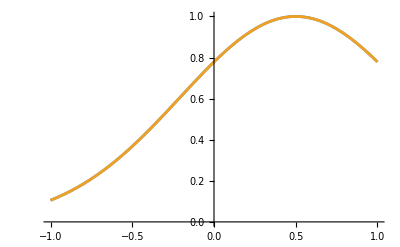

```mathematica
Plot[{f[x],approx[x]},{x,-1,1}]
```

```mathematica
xs = Table[2(i-1)/9-1,{i,1,10}];
xsCh = Table[Cos[(i-1)/(10-1)π],{i,1,10}];
fs = f/@xs;
```

```mathematica
B = Table[LegendreP[j-1,xs[[i]]],{i,1,10},{j,1,10}];
```

```mathematica
c2 = LinearSolve[B,fs]
```

{1/(89600 ⅇ^(9/4))(2857+15741 ⅇ^(50/81)+1080 ⅇ^(92/81)+19344 ⅇ^(14/9)+5778 ⅇ^(152/81)+2857 ⅇ^2+5778 ⅇ^(170/81)+15741 ⅇ^(176/81)+19344 ⅇ^(20/9)+1080 ⅇ^(182/81)),1/(985600 ⅇ^(9/4))(-85631-481869 ⅇ^(50/81)+291600 ⅇ^(92/81)-939384 ⅇ^(14/9)+1068714 ⅇ^(152/81)+85631 ⅇ^2-1068714 ⅇ^(170/81)+481869 ⅇ^(176/81)+939384 ⅇ^(20/9)-291600 ⅇ^(182/81)),-1/(98560 ⅇ^(9/4))3 (-4517-16803 ⅇ^(50/81)+14490 ⅇ^(92/81)-8362 ⅇ^(14/9)+15192 ⅇ^(152/81)-4517 ⅇ^2+15192 ⅇ^(170/81)-16803 ⅇ^(176/81)-8362 ⅇ^(20/9)+14490 ⅇ^(182/81)),-1/(6406400 ⅇ^(9/4))9 (112289+298161 ⅇ^(50/81)-794610 ⅇ^(92/81)+754446 ⅇ^(14/9)-1388016 ⅇ^(152/81)-112289 ⅇ^2+1388016 ⅇ^(170/81)-298161 ⅇ^(176/81)-754446 ⅇ^(20/9)+794610 ⅇ^(182/81)),-(729 (-744-187 ⅇ^(50/81)+3515 ⅇ^(92/81)-1983 ⅇ^(14/9)-601 ⅇ^(152/81)-744 ⅇ^2-601 ⅇ^(170/81)-187 ⅇ^(176/81)-1983 ⅇ^(20/9)+3515 ⅇ^(182/81)))/(3203200 ⅇ^(9/4)),-(243 (179-276 ⅇ^(50/81)-561 ⅇ^(92/81)+1299 ⅇ^(14/9)-771 ⅇ^(152/81)-179 ⅇ^2+771 ⅇ^(170/81)+276 ⅇ^(176/81)-1299 ⅇ^(20/9)+561 ⅇ^(182/81)))/(291200 ⅇ^(9/4)),(19683 (3-11 ⅇ^(50/81)+10 ⅇ^(92/81)+6 ⅇ^(14/9)-8 ⅇ^(152/81)+3 ⅇ^2-8 ⅇ^(170/81)-11 ⅇ^(176/81)+6 ⅇ^(20/9)+10 ⅇ^(182/81)))/(492800 ⅇ^(9/4)),(59049 (-31+177 ⅇ^(50/81)-402 ⅇ^(92/81)+462 ⅇ^(14/9)-336 ⅇ^(152/81)+31 ⅇ^2+336 ⅇ^(170/81)-177 ⅇ^(176/81)-462 ⅇ^(20/9)+402 ⅇ^(182/81)))/(21781760 ⅇ^(9/4)),(531441 (1-7 ⅇ^(50/81)+20 ⅇ^(92/81)-28 ⅇ^(14/9)+14 ⅇ^(152/81)+ⅇ^2+14 ⅇ^(170/81)-7 ⅇ^(176/81)-28 ⅇ^(20/9)+20 ⅇ^(182/81)))/(12812800 ⅇ^(9/4)),(4782969 (-1+9 ⅇ^(50/81)-36 ⅇ^(92/81)+84 ⅇ^(14/9)-126 ⅇ^(152/81)+ⅇ^2+126 ⅇ^(170/81)-9 ⅇ^(176/81)-84 ⅇ^(20/9)+36 ⅇ^(182/81)))/(217817600 ⅇ^(9/4))}

```mathematica
c2-c1//N
```

{3.76793×10^-6,-5.47892×10^-6,0.0000154465,-8.67506×10^-6,0.0000146183,-4.15271×10^-6,-1.30073×10^-6,5.04962×10^-6,-0.0000183252,9.20033×10^-6}

```mathematica
approx2[x_] := Sum[c2[[i]]LegendreP[i-1,x],{i,1,10}]
```

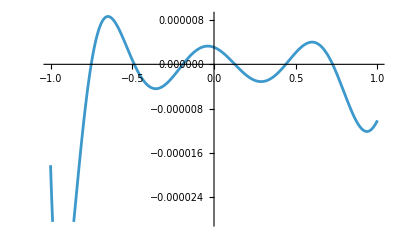

```mathematica
Plot[{approx[x]-approx2[x]},{x,-1,1}]
```

```mathematica
lj[j_,x_,ys_]:=Product[If[i!=j,(x-ys[[i]])/(ys[[j]]-ys[[i]]),1],{i,1,Length[ys]}]
```

```mathematica
resultsEquispaced={};
resultsChebyshev={};
Monitor[For[deg=5,deg<=15,deg+=1,
xs = Table[2(i-1)/(deg-1)-1,{i,1,deg}];
xsCh = Table[Cos[(i-1)/(deg-1)π],{i,1,deg}];

s = SingularValueList[Table[NIntegrate[lj[i,x,xs]lj[j,x,xs],{x,-1,1}],{i,1,Length[xs]},{j,1,Length[xs]}]];
κ = Max[s]/Min[s];
AppendTo[resultsEquispaced,{deg,κ}];

s = SingularValueList[Table[NIntegrate[lj[i,x,xsCh]lj[j,x,xsCh],{x,-1,1}],{i,1,Length[xs]},{j,1,Length[xs]}]];
κ = Max[s]/Min[s];
AppendTo[resultsChebyshev,{deg,κ}];
],deg]
```

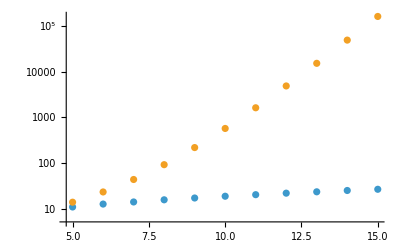

```mathematica
ListLogPlot[{resultsChebyshev,resultsEquispaced},PlotRange->All]
```

```mathematica
geomean[j_,ys_]:=Power[Product[If[i!=j,Abs[ys[[j]]-ys[[i]]],1],{i,1,Length[ys]}],1/(Length[ys]-1)]
```

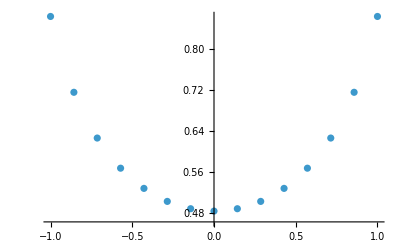

```mathematica
Table[{xs[[i]],geomean[i,xs]},{i,1,Length[xs]}]//N;
ListPlot[%,Joined->False,PlotRange->All]
```

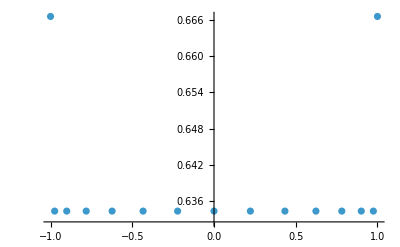

```mathematica
Table[{xsCh[[i]],geomean[i,xsCh]},{i,1,Length[xsCh]}]//N;
ListPlot[%,Joined->False,PlotRange->All]
```